```mathematica
S:=q/(2 m^2 γ0)(κ^2+ω0^2+γ0 κ+b^2)/κ^2
R:=q/(2 m^2 γ0 ω0^2)(κ^2+ω0^2)/κ^2
H:=-q/(2 m^2 γ0)b/κ^2
```

```mathematica
W=20;
```

```mathematica
Manipulate[Plot[Evaluate[{S,R,H}/.{q->1,m->1,ω0->1,γ0->g0,κ->k,b->b1}],{k,1,10}, PlotRange->All],{{b1,1},0,W},{{g0,1},0,W}]
```

```mathematica
V[r_,A_,B_]:=1/4 B r^4-1/2 A r^2
```

```mathematica
V[x_,A_,B_,C_,D_,F_]:=1/4 B x^4-1/2 A x^2+C Cos[F x]Exp[-x^2 D]
```

```mathematica
Simplify[2D[V[√r2,a,b,c,d,f],r2]]
```

-a+b r2-2 c d ⅇ^(-d r2) Cos[f √r2]-(c ⅇ^(-d r2) f Sin[f √r2])/(√r2)

```mathematica
Manipulate[Plot[{V[x,A,B,C1,D1,F],V[x,-1,0]},{x,-5,5},PlotRange->{Automatic,{-25,13}}],{{A,-1},-5,5},{{B,0},-5,5},{{C1,0},-5,5},{{D1,0},0,5},{{F,0},0,10}]
```

```mathematica
4
```

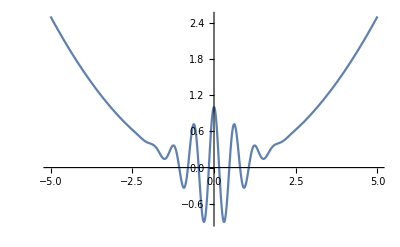

```mathematica
Plot[Cos[10x]Exp[-x^2] + 0.1 x^2,{x,-5,5}, PlotRange->All]
```

```mathematica
1/0.14/2
```

3.57143